# shooting method

## analytics

## derive eom

### definitions

```mathematica
Unprotect[Laplacian];
```

```mathematica
<<EDCRGTCcode.m;
xIN={r,t,x,y};
g0=DiagonalMatrix[{1/f[r], -f[r], r^2, r^2  }];

δg = ⅇ^(-ⅈ ω t) r^2 htx[r] SparseArray[{{2,3}-> 1,{3,2}-> 1}, 4];

g = Series[g0 + ϵ δg , {ϵ,0,1}]

RGtensors[g,xIN];
```

{{1/f[r],0,0,0},{0,-f[r],ⅇ^(-ⅈ t ω) r^2 htx[r] ϵ+O[ϵ]^2,0},{0,ⅇ^(-ⅈ t ω) r^2 htx[r] ϵ+O[ϵ]^2,r^2,0},{0,0,0,r^2}}

gdd = (1/f[r] | 0 | 0 | 0
0 | -f[r] | ⅇ^(-ⅈ t ω) r^2 htx[r] ϵ+O[ϵ]^2 | 0
0 | ⅇ^(-ⅈ t ω) r^2 htx[r] ϵ+O[ϵ]^2 | r^2 | 0
0 | 0 | 0 | r^2)

LineElement = (r^2 d[x]^2+r^2 d[y]^2+d[r]^2/f[r]-d[t]^2 f[r])+2 ⅇ^(-ⅈ t ω) r^2 d[t] d[x] htx[r] ϵ+O[ϵ]^2

gUU = (f[r]+O[ϵ]^3 | 0 | 0 | 0
0 | -1/f[r]+(ⅇ^(-2 ⅈ t ω) r^2 htx[r]^2 ϵ^2)/f[r]^2+O[ϵ]^3 | (ⅇ^(-ⅈ t ω) htx[r] ϵ)/f[r]+O[ϵ]^2 | 0
0 | (ⅇ^(-ⅈ t ω) htx[r] ϵ)/f[r]+O[ϵ]^2 | 1/r^2-(ⅇ^(-2 ⅈ t ω) htx[r]^2 ϵ^2)/f[r]+O[ϵ]^3 | 0
0 | 0 | 0 | 1/r^2+O[ϵ]^3)

gUU computed in 0.006455 sec

Gamma computed in 0.026425 sec

Riemann(dddd) computed in 0.052935 sec

Riemann(Uddd) computed in 0.082443 sec

Ricci computed in 0.056503 sec

Weyl computed in 0.180073 sec

Einstein computed in 0.013922 sec

All tasks completed in 0.429318 seconds

```mathematica
Ad= Series[ {0,At[r],0,0}+ ϵ ⅇ^(-ⅈ ω t) {0,0,ax[r],0}, {ϵ,0,1}];

Fdd=-covD[Ad]+ Transpose[covD[Ad]];
FUU= Raise[Fdd,1,2];
FdU=Raise[Fdd,2];
FUd=Raise[Fdd,1];
F2= multiDot[Fdd,FUU,{1,1},{2,2}];
```

```mathematica
EU =  covDiv[FUU,{2,{1}}];

Einsdd=Rdd - 1/2 R gdd - 3 gdd  - 1/2(multiDot[Fdd,FdU,{2,2}] - 1/4 F2 gdd );
```

```mathematica
soln = {At-> Function[r, μ(1- rH/r) ],  f-> Function[r, r^2-m0/r  +(rH^2 μ^2)/(4 r^2) ]};
```

```mathematica
Simplify[  {EU,Einsdd} /. ϵ-> 0  /. soln ]
```

{{0,0,0,0},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

### find decoupled eom

```mathematica
vars = Flatten[ Table[ D[{ax[r],htx[r]}, {r,i}] , {i,0,2}]];
```

```mathematica
e1 = Collect[ ⅇ^(ⅈ t ω) D[EU[[3]], ϵ] /. ϵ-> 0 , vars, Simplify]
```

(ω^2 ax[r])/(r^2 f[r])+(ax'[r] f'[r])/r^2+At'[r] htx'[r]+htx[r] ((2 At'[r])/r+At''[r])+(f[r] ax''[r])/r^2

```mathematica
e2 = Collect[ ⅇ^(ⅈ t ω) D[Einsdd[[1,3]], ϵ] /. ϵ-> 0 , vars, Simplify]
```

(ⅈ ω ax[r] At'[r])/(2 f[r])+(ⅈ r^2 ω htx'[r])/(2 f[r])

```mathematica
repAtPP = Solve[ Simplify[EU[[2]] /. ϵ-> 0 ] == 0 , At''[r] ][[1]];
```

```mathematica
eqaux = Collect[r^2 (e1 + (2 ⅈ f[r] At'[r])/(r^2 ω)  e2) /. repAtPP , vars, Simplify ]
```

ax[r] (ω^2/f[r]-At'[r]^2)+ax'[r] f'[r]+f[r] ax''[r]

### simplify eom

```mathematica
repm0 = Solve[ Simplify[f[rH] /. soln] == 0 , m0][[1]];
```

```mathematica
repr = {r-> rH/z, μ-> μ1 rH, ω-> ω1 rH }; repfields = {ax-> Function[x, ax[rH/x]]};
```

```mathematica
eq1aux = Collect[(1/4 z^2)^-1(4+z^4 μ1^2-z^3 (4+μ1^2))^-1 eqaux /. soln /. repm0  /. repr  /. repfields ,Flatten[ {vars, ω1 }]/. r-> z, Simplify];
```

```mathematica
repγ = {γ-> 4/(12 - μ1^2)};
```

```mathematica
Collect[ Series[x^2 (1-z^2)^(ⅈ ω1 γ) eq1aux /. ax-> Function[z , (1-z^2)^(-ⅈ ω1 γ)  aax[z] ]  /. z-> 1 - x , {x,0,0} ] /. repγ , x, Simplify]
```

0

```mathematica
Collect[  (1-z^2)^(ⅈ ω1 γ) eq1aux /. ax-> Function[z , (1-z^2)^(-ⅈ ω1 γ)  aax[z] ] /. repγ ,{aax''[z],aax'[z], aax[z]} , Simplify]
```

(-(4 z^2 μ1^2)/(4+z^4 μ1^2-z^3 (4+μ1^2))+(8 ⅈ ω1)/((-1+z^2) (-12+μ1^2))+(8 ⅈ z^3 (-12+(-3+4 z) μ1^2) ω1)/((-1+z^2) (-12+μ1^2) (4+z^4 μ1^2-z^3 (4+μ1^2)))-(16 ⅈ z^2 (-12+μ1^2-4 ⅈ ω1) ω1)/((-1+z^2)^2 (-12+μ1^2)^2)+(16 ω1^2)/((4+z^4 μ1^2-z^3 (4+μ1^2))^2)) aax[z]+(z (4 z^3 μ1^2 (-12+μ1^2+4 ⅈ ω1)+z (144+24 μ1^2-3 μ1^4-64 ⅈ ω1)+z^2 (144-24 μ1^2+μ1^4-64 ⅈ ω1)-64 ⅈ ω1) aax'[z])/((-1+z) (1+z) (-12+μ1^2) (-4-4 z-4 z^2+z^3 μ1^2))+aax''[z]

## UV asymptotics

```mathematica
EQ1 = (-(4 z^2 μ1^2)/(4+z^4 μ1^2-z^3 (4+μ1^2))+(8 ⅈ ω1)/((-1+z^2) (-12+μ1^2))+(8 ⅈ z^3 (-12+(-3+4 z) μ1^2) ω1)/((-1+z^2) (-12+μ1^2) (4+z^4 μ1^2-z^3 (4+μ1^2)))-(16 ⅈ z^2 (-12+μ1^2-4 ⅈ ω1) ω1)/((-1+z^2)^2 (-12+μ1^2)^2)+(16 ω1^2)/((4+z^4 μ1^2-z^3 (4+μ1^2))^2)) aax[z]+(z (4 z^3 μ1^2 (-12+μ1^2+4 ⅈ ω1)+z (144+24 μ1^2-3 μ1^4-64 ⅈ ω1)+z^2 (144-24 μ1^2+μ1^4-64 ⅈ ω1)-64 ⅈ ω1) aax'[z])/((-1+z) (1+z) (-12+μ1^2) (-4-4 z-4 z^2+z^3 μ1^2))+aax''[z];
```

```mathematica
aaxSuv[z_]= Sum[ auv[i] z^i, {i,0,10}];
```

```mathematica
UVasympt = {aax-> aaxSuv};
```

work out coefficients

```mathematica
UVcoeff={auv[0]->a0,auv[1]->a1};
```

```mathematica
For[ b = 0 , b≤ 8 , b++ , 
eqtempUV = Collect[ Series[ EQ1 /.  UVasympt , {z,0,b}] /. UVcoeff , z, Simplify];
solntempUV = Solve[eqtempUV == 0 , auv[b+2] ][[1]]; 
UVcoeff = Simplify[ Flatten[  Append[ UVcoeff, solntempUV ]  ]] ;
];
```

#### UV coeff

```mathematica
UVcoeff={auv[0]->a0,auv[1]->a1,auv[2]->1/2 a0 ((8 ⅈ)/(-12+μ1^2)-ω1) ω1,auv[3]->a1 ((4 ⅈ ω1)/(-12+μ1^2)-ω1^2/6),auv[4]->(3 a1 (-12+μ1^2)^2 (4+μ1^2)+2 a0 (2 μ1^6+48 ω1 (-12 ⅈ-4 ω1+12 ⅈ ω1^2+3 ω1^3)+μ1^4 (-48+ω1^4)-24 μ1^2 (-12-2 ⅈ ω1+2 ⅈ ω1^3+ω1^4)))/(48 (-12+μ1^2)^2),auv[5]->(ω1 (-15 a0 (-12+μ1^2)^2 (4+μ1^2) ω1+2 a1 (μ1^4 ω1^3-8 μ1^2 (-30 ⅈ+10 ⅈ ω1^2+3 ω1^3)+48 (-60 ⅈ-20 ω1+20 ⅈ ω1^2+3 ω1^3))))/(240 (-12+μ1^2)^2),auv[6]->1/(1440 (-12+μ1^2)^3)ω1 (-45 a1 (-12+μ1^2)^2 (4+μ1^2) (-8 ⅈ+(-12+μ1^2) ω1)+2 a0 (22 μ1^8 ω1-μ1^6 (-240 ⅈ+792 ω1+ω1^5)+12 μ1^4 (-400 ⅈ+792 ω1-60 ⅈ ω1^2+10 ⅈ ω1^4+3 ω1^5)-144 μ1^2 (-80 ⅈ+304 ω1-120 ⅈ ω1^2-20 ω1^3+20 ⅈ ω1^4+3 ω1^5)+192 (720 ⅈ+360 ω1-580 ⅈ ω1^2-180 ω1^3+90 ⅈ ω1^4+9 ω1^5))),auv[7]->1/(10080 (-12+μ1^2)^3)(15 a0 (-12+μ1^2)^2 (4+μ1^2) (8 μ1^4-84 ω1^3 (2 ⅈ+ω1)+μ1^2 (-96+7 ω1^4))+2 a1 (45 μ1^10+20 μ1^8 (-63+5 ω1^2)-μ1^6 (-7200+3600 ω1^2+ω1^6)+12 μ1^4 (4320+560 ⅈ ω1+3600 ω1^2-140 ⅈ ω1^3+14 ⅈ ω1^5+3 ω1^6)-48 μ1^2 (6480+3360 ⅈ ω1+4440 ω1^2-840 ⅈ ω1^3-140 ω1^4+84 ⅈ ω1^5+9 ω1^6)+192 (-6480+5040 ⅈ ω1+2520 ω1^2-1540 ⅈ ω1^3-420 ω1^4+126 ⅈ ω1^5+9 ω1^6))),auv[8]->1/(161280 (-12+μ1^2)^4)(-60 a1 (-12+μ1^2)^2 (4+μ1^2) (18 μ1^6-336 ω1 (-12 ⅈ-4 ω1+12 ⅈ ω1^2+3 ω1^3)-μ1^4 (432+7 ω1^4)+24 μ1^2 (108-14 ⅈ ω1+14 ⅈ ω1^3+7 ω1^4))+a0 (-45 μ1^12 (32+39 ω1^2)-8 μ1^10 (-8640-8775 ω1^2+146 ω1^4)-3072 μ1^2 ω1 (-7560 ⅈ+27390 ω1+27048 ⅈ ω1^2+12924 ω1^3-2170 ⅈ ω1^4-420 ω1^5+126 ⅈ ω1^6+9 ω1^7)+3072 ω1 (-90720 ⅈ-244980 ω1+70560 ⅈ ω1^2+30800 ω1^3-10920 ⅈ ω1^4-2520 ω1^5+504 ⅈ ω1^6+27 ω1^7)+4 μ1^8 (-311040+6720 ⅈ ω1-217620 ω1^2+4928 ⅈ ω1^3+14016 ω1^4+ω1^8)-64 μ1^6 (-155520+12600 ⅈ ω1-19380 ω1^2+12768 ⅈ ω1^3+15768 ω1^4-210 ⅈ ω1^5+14 ⅈ ω1^7+3 ω1^8)+384 μ1^4 (-77760+15120 ⅈ ω1+98410 ω1^2+32256 ⅈ ω1^3+22704 ω1^4-1260 ⅈ ω1^5-140 ω1^6+84 ⅈ ω1^7+9 ω1^8))),auv[9]->1/(1451520 (-12+μ1^2)^4)ω1 (36 a0 (-12+μ1^2)^2 (4+μ1^2) (572 μ1^6 ω1-1008 ω1^2 (-60 ⅈ-20 ω1+20 ⅈ ω1^2+3 ω1^3)-3 μ1^4 (-640 ⅈ+4576 ω1+7 ω1^5)+24 μ1^2 (-960 ⅈ+3432 ω1-210 ⅈ ω1^2+70 ⅈ ω1^4+21 ω1^5))+a1 (-9315 μ1^12 ω1-8 μ1^10 (-6480 ⅈ-46575 ω1+344 ω1^3)+4 μ1^8 (-362880 ⅈ-1155060 ω1+28800 ⅈ ω1^2+33024 ω1^3+ω1^7)-192 μ1^6 (-50760 ⅈ-37260 ω1+23280 ⅈ ω1^2+12384 ω1^3-126 ⅈ ω1^4+6 ⅈ ω1^6+ω1^7)+3456 μ1^4 (2160 ⅈ+52810 ω1+17760 ⅈ ω1^2+6064 ω1^3-252 ⅈ ω1^4-28 ω1^5+12 ⅈ ω1^6+ω1^7)-9216 μ1^2 (-29160 ⅈ+28170 ω1+39240 ⅈ ω1^2+11232 ω1^3-1414 ⅈ ω1^4-252 ω1^5+54 ⅈ ω1^6+3 ω1^7)+27648 (-142560 ⅈ-167220 ω1+30240 ⅈ ω1^2+10640 ω1^3-2632 ⅈ ω1^4-504 ω1^5+72 ⅈ ω1^6+3 ω1^7))),auv[10]->1/(14515200 (-12+μ1^2)^5)(180 a1 (-12+μ1^2)^2 (4+μ1^2) (126 μ1^10+6 μ1^8 (-588+127 ω1^2)-μ1^6 (-20160+2160 ⅈ ω1+27432 ω1^2+7 ω1^6)+1344 (-2592+720 ⅈ ω1+360 ω1^2-580 ⅈ ω1^3-180 ω1^4+90 ⅈ ω1^5+9 ω1^6)+12 μ1^4 (12096+4880 ⅈ ω1+27432 ω1^2-420 ⅈ ω1^3+70 ⅈ ω1^5+21 ω1^6)-144 μ1^2 (6048+3280 ⅈ ω1+9424 ω1^2-840 ⅈ ω1^3-140 ω1^4+140 ⅈ ω1^5+21 ω1^6))+a0 (30240 μ1^16+5 μ1^14 (-314496-13376 ω1^2+7155 ω1^4)+4 μ1^12 (7378560-129600 ⅈ ω1+1003200 ω1^2-157950 ⅈ ω1^3-465075 ω1^4+1412 ω1^6)+110592 ω1 (2177280 ⅈ+1512000 ω1-3609000 ⅈ ω1^2-2153100 ω1^3+303520 ⅈ ω1^4+84000 ω1^5-15960 ⅈ ω1^6-2520 ω1^7+270 ⅈ ω1^8+9 ω1^9)-4 μ1^10 (50803200-6624000 ⅈ ω1+24076800 ω1^2-6539760 ⅈ ω1^3-8729100 ω1^4+105120 ⅈ ω1^5+84720 ω1^6+ω1^10)+240 μ1^8 (-1451520-2140416 ⅈ ω1+4775040 ω1^2-1513368 ⅈ ω1^3-1016484 ω1^4+87456 ⅈ ω1^5+33888 ω1^6-168 ⅈ ω1^7+6 ⅈ ω1^9+ω1^10)-5760 μ1^6 (-1596672-767232 ⅈ ω1+1160160 ω1^2-275536 ⅈ ω1^3+40134 ω1^4+69792 ⅈ ω1^5+17784 ω1^6-336 ⅈ ω1^7-28 ω1^8+12 ⅈ ω1^9+ω1^10)+23040 μ1^4 (-435456-514944 ⅈ ω1+692064 ω1^2+32028 ⅈ ω1^3+322542 ω1^4+161424 ⅈ ω1^5+32976 ω1^6-1792 ⅈ ω1^7-252 ω1^8+54 ⅈ ω1^9+3 ω1^10)-27648 μ1^2 (4354560+1693440 ⅈ ω1+907200 ω1^2-1384080 ⅈ ω1^3-635260 ω1^4+617760 ⅈ ω1^5+129232 ω1^6-15680 ⅈ ω1^7-2520 ω1^8+360 ⅈ ω1^9+15 ω1^10)))};
```

```mathematica
Collect[ Series[ EQ1 /.  UVasympt , {z,0,8}] /. UVcoeff , z, Simplify]
```

0

## IR asymptotics

```mathematica
EQ1 = (-(4 z^2 μ1^2)/(4+z^4 μ1^2-z^3 (4+μ1^2))+(8 ⅈ ω1)/((-1+z^2) (-12+μ1^2))+(8 ⅈ z^3 (-12+(-3+4 z) μ1^2) ω1)/((-1+z^2) (-12+μ1^2) (4+z^4 μ1^2-z^3 (4+μ1^2)))-(16 ⅈ z^2 (-12+μ1^2-4 ⅈ ω1) ω1)/((-1+z^2)^2 (-12+μ1^2)^2)+(16 ω1^2)/((4+z^4 μ1^2-z^3 (4+μ1^2))^2)) aax[z]+(z (4 z^3 μ1^2 (-12+μ1^2+4 ⅈ ω1)+z (144+24 μ1^2-3 μ1^4-64 ⅈ ω1)+z^2 (144-24 μ1^2+μ1^4-64 ⅈ ω1)-64 ⅈ ω1) aax'[z])/((-1+z) (1+z) (-12+μ1^2) (-4-4 z-4 z^2+z^3 μ1^2))+aax''[z];
```

```mathematica
aaxSir[z_]= Sum[ air[i] (1-z)^i, {i,0,5}];
```

```mathematica
IRasympt = {aax-> aaxSir};
```

work out coefficients

```mathematica
IRcoeff = {air[0]-> axH };

For[ b = 0 , b≤ 4 , b++ , 
eqtempIR = Collect[ Series[ x  EQ1 /.  IRasympt /. z-> 1 - x , {x,0,b}] /.IRcoeff , x, Simplify];
solntempIR = Solve[eqtempIR == 0 , air[b+1] ][[1]]; 
IRcoeff = Simplify[ Flatten[  Append[ IRcoeff, solntempIR ]  ]] ;
];
```

#### IR coeff

```mathematica
IRcoeff={air[0]->axH,air[1]->-(2 axH (2 μ1^6+μ1^4 (-48-7 ⅈ ω1)-144 ω1 (3 ⅈ+2 ω1)+8 μ1^2 (36+15 ⅈ ω1+7 ω1^2)))/((-12+μ1^2)^2 (-12+μ1^2+8 ⅈ ω1)),air[2]->-((axH ω1 (55 ⅈ μ1^10+4 μ1^8 (-505 ⅈ+12 ω1)+16 ⅈ μ1^6 (1542+168 ⅈ ω1+197 ω1^2)-9216 (-99 ⅈ-180 ω1+103 ⅈ ω1^2+18 ω1^3)+768 μ1^2 (-207 ⅈ-648 ω1+557 ⅈ ω1^2+84 ω1^3)-64 μ1^4 (1458 ⅈ-864 ω1+1045 ⅈ ω1^2+98 ω1^3)))/(2 (-12+μ1^2)^4 (μ1^4+12 ⅈ μ1^2 (2 ⅈ+ω1)-16 (-9+9 ⅈ ω1+2 ω1^2)))),air[3]->(axH ω1 (-273 ⅈ μ1^16+2 μ1^14 (7368 ⅈ+1283 ω1)-24 ⅈ μ1^12 (12048-4985 ⅈ ω1+1004 ω1^2)+32 μ1^10 (62856 ⅈ+59295 ω1+38040 ⅈ ω1^2+8369 ω1^3)+384 ⅈ μ1^8 (23220+17853 ⅈ ω1-66852 ω1^2+25681 ⅈ ω1^3+2072 ω1^4)+2654208 (1782 ⅈ+4851 ω1-4788 ⅈ ω1^2-2167 ω1^3+456 ⅈ ω1^4+36 ω1^5)-221184 μ1^2 (14904 ⅈ+33489 ω1-35208 ⅈ ω1^2-16479 ω1^3+3488 ⅈ ω1^4+252 ω1^5)+18432 μ1^4 (69984 ⅈ+89415 ω1-109692 ⅈ ω1^2-53286 ω1^3+10288 ⅈ ω1^4+588 ω1^5)-512 μ1^6 (433512 ⅈ+255447 ω1-578448 ⅈ ω1^2-272730 ω1^3+40416 ⅈ ω1^4+1372 ω1^5)))/(6 (-12+μ1^2)^6 (3 μ1^6+μ1^4 (-108+44 ⅈ ω1)-48 μ1^2 (-27+22 ⅈ ω1+4 ω1^2)-64 ⅈ (-81 ⅈ-99 ω1+36 ⅈ ω1^2+4 ω1^3))),air[4]->-((ⅈ axH ω1 (1767 μ1^22+4 ⅈ μ1^20 (29127 ⅈ+8002 ω1)+4 μ1^18 (641700-554160 ⅈ ω1+28457 ω1^2)+16 ⅈ μ1^16 (135108 ⅈ+3855528 ω1+605715 ⅈ ω1^2+219077 ω1^3)-64 μ1^14 (14865768+12939840 ⅈ ω1-5751108 ω1^2+3406344 ⅈ ω1^3+337711 ω1^4)+256 μ1^12 (79157736+15342480 ⅈ ω1-32083740 ω1^2+22722780 ⅈ ω1^3+4349499 ω1^4-234727 ⅈ ω1^5)+1024 μ1^10 (-206120376+35621856 ⅈ ω1+116309358 ω1^2-86154264 ⅈ ω1^3-23289363 ω1^4+2421582 ⅈ ω1^5+77420 ω1^6)+21233664 μ1^2 (-801900+2805840 ⅈ ω1+4107105 ω1^2-2858472 ⅈ ω1^3-1079409 ω1^4+224270 ⅈ ω1^5+23964 ω1^6-1008 ⅈ ω1^7)+1769472 μ1^4 (5502492-12665160 ⅈ ω1-19048932 ω1^2+13354164 ⅈ ω1^3+4992723 ω1^4-990843 ⅈ ω1^5-96952 ω1^6+3528 ⅈ ω1^7)+147456 μ1^6 (-29944404+34997184 ⅈ ω1+52584660 ω1^2-37369656 ⅈ ω1^3-13474965 ω1^4+2409796 ⅈ ω1^5+197816 ω1^6-5488 ⅈ ω1^7)+4096 μ1^8 (307317240-171091440 ⅈ ω1-285024906 ω1^2+207974574 ⅈ ω1^3+68212863 ω1^4-10016097 ⅈ ω1^5-599508 ω1^6+9604 ⅈ ω1^7)+254803968 ⅈ (-72900 ⅈ-288360 ω1+403353 ⅈ ω1^2+277047 ω1^3-104295 ⅈ ω1^4-21925 ω1^5+2412 ⅈ ω1^6+108 ω1^7)))/(48 (-12+μ1^2)^8 (3 μ1^8+μ1^6 (-144+50 ⅈ ω1)-8 μ1^4 (-324+225 ⅈ ω1+35 ω1^2)+32 μ1^2 (-648+675 ⅈ ω1+210 ω1^2-20 ⅈ ω1^3)+128 (486-675 ⅈ ω1-315 ω1^2+60 ⅈ ω1^3+4 ω1^4)))),air[5]->-((ⅈ axH ω1 (20565 μ1^28+μ1^26 (-1514160+589629 ⅈ ω1)-4 μ1^24 (-7198740+13402167 ⅈ ω1+40645 ω1^2)+4 μ1^22 (209433600+521508696 ⅈ ω1-3865640 ω1^2+14909655 ⅈ ω1^3)-48 μ1^20 (1175634000+929669112 ⅈ ω1-47509040 ω1^2+106095425 ⅈ ω1^3+11725795 ω1^4)+64 μ1^18 (22061056320+8612346492 ⅈ ω1-1689085560 ω1^2+3027053505 ⅈ ω1^3+662471810 ω1^4-38947175 ⅈ ω1^5)+768 μ1^16 (-26994753360-4564130652 ⅈ ω1+3712317300 ω1^2-5686880415 ⅈ ω1^3-1826348755 ω1^4+213521747 ⅈ ω1^5+8120725 ω1^6)+2048 μ1^14 (95007479040+782333640 ⅈ ω1-23749501320 ω1^2+32120580915 ⅈ ω1^3+13201267740 ω1^4-2279144526 ⅈ ω1^5-170781350 ω1^6+4389035 ⅈ ω1^7)-8192 μ1^12 (142825359240-18735469128 ⅈ ω1-70460046720 ω1^2+86720610015 ⅈ ω1^3+41642979705 ω1^4-9286000218 ⅈ ω1^5-1016926860 ω1^6+50632395 ⅈ ω1^7+847210 ω1^8)+1019215872 μ1^2 (18895680-436901364 ⅈ ω1-1036064520 ω1^2+1017620415 ⅈ ω1^3+548549910 ω1^4-177227973 ⅈ ω1^5-35208620 ω1^6+4202110 ⅈ ω1^7+275400 ω1^8-7560 ⅈ ω1^9)+84934656 μ1^4 (83455920+1977112152 ⅈ ω1+5966544240 ω1^2-6130664415 ⅈ ω1^3-3338077365 ω1^4+1065188484 ⅈ ω1^5+205270720 ω1^6-23309730 ⅈ ω1^7-1421580 ω1^8+35280 ⅈ ω1^9)+32768 μ1^10 (129501542880-39940284330 ⅈ ω1-151879830840 ω1^2+175490108145 ⅈ ω1^3+91808755830 ω1^4-24238440297 ⅈ ω1^5-3393054870 ω1^6+242385255 ⅈ ω1^7+7627340 ω1^8-67228 ⅈ ω1^9)+393216 μ1^8 (-19479084120+17924087754 ⅈ ω1+81174784230 ω1^2-90087682815 ⅈ ω1^3-48852978255 ω1^4+14305233717 ⅈ ω1^5+2352002565 ω1^6-210938685 ⅈ ω1^7-9252250 ω1^8+144060 ⅈ ω1^9)+2359296 μ1^6 (755827200-15795371304 ⅈ ω1-64243125000 ω1^2+68843966715 ⅈ ω1^3+37639901880 ω1^4-11670104268 ⅈ ω1^5-2121538980 ω1^6+220218930 ⅈ ω1^7+11839120 ω1^8-246960 ⅈ ω1^9)+12230590464 ⅈ (4723920 ⅈ+41235156 ω1-83425140 ⅈ ω1^2-78691905 ω1^3+41892885 ⅈ ω1^4+13565241 ω1^5-2727235 ⅈ ω1^6-332490 ω1^7+22500 ⅈ ω1^8+648 ω1^9)))/(120 (-12+μ1^2)^10 (15 μ1^10+μ1^8 (-900+274 ⅈ ω1)-24 μ1^6 (-900+548 ⅈ ω1+75 ω1^2)+32 μ1^4 (-8100+7398 ⅈ ω1+2025 ω1^2-170 ⅈ ω1^3)+384 μ1^2 (4050-4932 ⅈ ω1-2025 ω1^2+340 ⅈ ω1^3+20 ω1^4)+512 ⅈ (7290 ⅈ+11097 ω1-6075 ⅈ ω1^2-1530 ω1^3+180 ⅈ ω1^4+8 ω1^5))))};
```

```mathematica
Collect[ Series[ EQ1 /.  IRasympt /. z-> 1 - x, {x,0,3}] /. IRcoeff , x, Simplify]
```

0

## numerics

## preliminaries

### message catch

this stops the integration if NDSolve finds a stiff system

```mathematica
NDSolve::ndsz="Could not perform the integration";

Unprotect[Message];
Message[mm :NDSolve::ndsz,m___]:=Block[{$inMsg=True,result},
Message[mm,m];

Abort[]]/;!TrueQ[$inMsg]
Protect[Message];
```

### eoms

this is the eom. it’s a good idea to write it as a function of the free parameters μ1 and ω1, which μ and ω normalized by rH

```mathematica
e1[μ1_,ω1_]= (-(4 z^2 μ1^2)/(4+z^4 μ1^2-z^3 (4+μ1^2))+(8 ⅈ ω1)/((-1+z^2) (-12+μ1^2))+(8 ⅈ z^3 (-12+(-3+4 z) μ1^2) ω1)/((-1+z^2) (-12+μ1^2) (4+z^4 μ1^2-z^3 (4+μ1^2)))-(16 ⅈ z^2 (-12+μ1^2-4 ⅈ ω1) ω1)/((-1+z^2)^2 (-12+μ1^2)^2)+(16 ω1^2)/((4+z^4 μ1^2-z^3 (4+μ1^2))^2)) aax[z]+(z (4 z^3 μ1^2 (-12+μ1^2+4 ⅈ ω1)+z (144+24 μ1^2-3 μ1^4-64 ⅈ ω1)+z^2 (144-24 μ1^2+μ1^4-64 ⅈ ω1)-64 ⅈ ω1) aax'[z])/((-1+z) (1+z) (-12+μ1^2) (-4-4 z-4 z^2+z^3 μ1^2))+aax''[z];
```

### asymptotics

this gives the asymptotic solution near z = 0, and z= 1 as a function of the UV and IR data

#### IR coeff

```mathematica
IRcoeff={air[0]->axH,air[1]->-((2 axH (2 μ1^6+μ1^4 (-48-7 ⅈ ω1)-144 ω1 (3 ⅈ+2 ω1)+8 μ1^2 (36+15 ⅈ ω1+7 ω1^2)))/((-12+μ1^2)^2 (-12+μ1^2+8 ⅈ ω1))),air[2]->-((axH ω1 (55 ⅈ μ1^10+4 μ1^8 (-505 ⅈ+12 ω1)+16 ⅈ μ1^6 (1542+168 ⅈ ω1+197 ω1^2)-9216 (-99 ⅈ-180 ω1+103 ⅈ ω1^2+18 ω1^3)+768 μ1^2 (-207 ⅈ-648 ω1+557 ⅈ ω1^2+84 ω1^3)-64 μ1^4 (1458 ⅈ-864 ω1+1045 ⅈ ω1^2+98 ω1^3)))/(2 (-12+μ1^2)^4 (μ1^4+12 ⅈ μ1^2 (2 ⅈ+ω1)-16 (-9+9 ⅈ ω1+2 ω1^2)))),air[3]->(axH ω1 (-273 ⅈ μ1^16+2 μ1^14 (7368 ⅈ+1283 ω1)-24 ⅈ μ1^12 (12048-4985 ⅈ ω1+1004 ω1^2)+32 μ1^10 (62856 ⅈ+59295 ω1+38040 ⅈ ω1^2+8369 ω1^3)+384 ⅈ μ1^8 (23220+17853 ⅈ ω1-66852 ω1^2+25681 ⅈ ω1^3+2072 ω1^4)+2654208 (1782 ⅈ+4851 ω1-4788 ⅈ ω1^2-2167 ω1^3+456 ⅈ ω1^4+36 ω1^5)-221184 μ1^2 (14904 ⅈ+33489 ω1-35208 ⅈ ω1^2-16479 ω1^3+3488 ⅈ ω1^4+252 ω1^5)+18432 μ1^4 (69984 ⅈ+89415 ω1-109692 ⅈ ω1^2-53286 ω1^3+10288 ⅈ ω1^4+588 ω1^5)-512 μ1^6 (433512 ⅈ+255447 ω1-578448 ⅈ ω1^2-272730 ω1^3+40416 ⅈ ω1^4+1372 ω1^5)))/(6 (-12+μ1^2)^6 (3 μ1^6+μ1^4 (-108+44 ⅈ ω1)-48 μ1^2 (-27+22 ⅈ ω1+4 ω1^2)-64 ⅈ (-81 ⅈ-99 ω1+36 ⅈ ω1^2+4 ω1^3))),air[4]->-((ⅈ axH ω1 (1767 μ1^22+4 ⅈ μ1^20 (29127 ⅈ+8002 ω1)+4 μ1^18 (641700-554160 ⅈ ω1+28457 ω1^2)+16 ⅈ μ1^16 (135108 ⅈ+3855528 ω1+605715 ⅈ ω1^2+219077 ω1^3)-64 μ1^14 (14865768+12939840 ⅈ ω1-5751108 ω1^2+3406344 ⅈ ω1^3+337711 ω1^4)+256 μ1^12 (79157736+15342480 ⅈ ω1-32083740 ω1^2+22722780 ⅈ ω1^3+4349499 ω1^4-234727 ⅈ ω1^5)+1024 μ1^10 (-206120376+35621856 ⅈ ω1+116309358 ω1^2-86154264 ⅈ ω1^3-23289363 ω1^4+2421582 ⅈ ω1^5+77420 ω1^6)+21233664 μ1^2 (-801900+2805840 ⅈ ω1+4107105 ω1^2-2858472 ⅈ ω1^3-1079409 ω1^4+224270 ⅈ ω1^5+23964 ω1^6-1008 ⅈ ω1^7)+1769472 μ1^4 (5502492-12665160 ⅈ ω1-19048932 ω1^2+13354164 ⅈ ω1^3+4992723 ω1^4-990843 ⅈ ω1^5-96952 ω1^6+3528 ⅈ ω1^7)+147456 μ1^6 (-29944404+34997184 ⅈ ω1+52584660 ω1^2-37369656 ⅈ ω1^3-13474965 ω1^4+2409796 ⅈ ω1^5+197816 ω1^6-5488 ⅈ ω1^7)+4096 μ1^8 (307317240-171091440 ⅈ ω1-285024906 ω1^2+207974574 ⅈ ω1^3+68212863 ω1^4-10016097 ⅈ ω1^5-599508 ω1^6+9604 ⅈ ω1^7)+254803968 ⅈ (-72900 ⅈ-288360 ω1+403353 ⅈ ω1^2+277047 ω1^3-104295 ⅈ ω1^4-21925 ω1^5+2412 ⅈ ω1^6+108 ω1^7)))/(48 (-12+μ1^2)^8 (3 μ1^8+μ1^6 (-144+50 ⅈ ω1)-8 μ1^4 (-324+225 ⅈ ω1+35 ω1^2)+32 μ1^2 (-648+675 ⅈ ω1+210 ω1^2-20 ⅈ ω1^3)+128 (486-675 ⅈ ω1-315 ω1^2+60 ⅈ ω1^3+4 ω1^4)))),air[5]->-((ⅈ axH ω1 (20565 μ1^28+μ1^26 (-1514160+589629 ⅈ ω1)-4 μ1^24 (-7198740+13402167 ⅈ ω1+40645 ω1^2)+4 μ1^22 (209433600+521508696 ⅈ ω1-3865640 ω1^2+14909655 ⅈ ω1^3)-48 μ1^20 (1175634000+929669112 ⅈ ω1-47509040 ω1^2+106095425 ⅈ ω1^3+11725795 ω1^4)+64 μ1^18 (22061056320+8612346492 ⅈ ω1-1689085560 ω1^2+3027053505 ⅈ ω1^3+662471810 ω1^4-38947175 ⅈ ω1^5)+768 μ1^16 (-26994753360-4564130652 ⅈ ω1+3712317300 ω1^2-5686880415 ⅈ ω1^3-1826348755 ω1^4+213521747 ⅈ ω1^5+8120725 ω1^6)+2048 μ1^14 (95007479040+782333640 ⅈ ω1-23749501320 ω1^2+32120580915 ⅈ ω1^3+13201267740 ω1^4-2279144526 ⅈ ω1^5-170781350 ω1^6+4389035 ⅈ ω1^7)-8192 μ1^12 (142825359240-18735469128 ⅈ ω1-70460046720 ω1^2+86720610015 ⅈ ω1^3+41642979705 ω1^4-9286000218 ⅈ ω1^5-1016926860 ω1^6+50632395 ⅈ ω1^7+847210 ω1^8)+1019215872 μ1^2 (18895680-436901364 ⅈ ω1-1036064520 ω1^2+1017620415 ⅈ ω1^3+548549910 ω1^4-177227973 ⅈ ω1^5-35208620 ω1^6+4202110 ⅈ ω1^7+275400 ω1^8-7560 ⅈ ω1^9)+84934656 μ1^4 (83455920+1977112152 ⅈ ω1+5966544240 ω1^2-6130664415 ⅈ ω1^3-3338077365 ω1^4+1065188484 ⅈ ω1^5+205270720 ω1^6-23309730 ⅈ ω1^7-1421580 ω1^8+35280 ⅈ ω1^9)+32768 μ1^10 (129501542880-39940284330 ⅈ ω1-151879830840 ω1^2+175490108145 ⅈ ω1^3+91808755830 ω1^4-24238440297 ⅈ ω1^5-3393054870 ω1^6+242385255 ⅈ ω1^7+7627340 ω1^8-67228 ⅈ ω1^9)+393216 μ1^8 (-19479084120+17924087754 ⅈ ω1+81174784230 ω1^2-90087682815 ⅈ ω1^3-48852978255 ω1^4+14305233717 ⅈ ω1^5+2352002565 ω1^6-210938685 ⅈ ω1^7-9252250 ω1^8+144060 ⅈ ω1^9)+2359296 μ1^6 (755827200-15795371304 ⅈ ω1-64243125000 ω1^2+68843966715 ⅈ ω1^3+37639901880 ω1^4-11670104268 ⅈ ω1^5-2121538980 ω1^6+220218930 ⅈ ω1^7+11839120 ω1^8-246960 ⅈ ω1^9)+12230590464 ⅈ (4723920 ⅈ+41235156 ω1-83425140 ⅈ ω1^2-78691905 ω1^3+41892885 ⅈ ω1^4+13565241 ω1^5-2727235 ⅈ ω1^6-332490 ω1^7+22500 ⅈ ω1^8+648 ω1^9)))/(120 (-12+μ1^2)^10 (15 μ1^10+μ1^8 (-900+274 ⅈ ω1)-24 μ1^6 (-900+548 ⅈ ω1+75 ω1^2)+32 μ1^4 (-8100+7398 ⅈ ω1+2025 ω1^2-170 ⅈ ω1^3)+384 μ1^2 (4050-4932 ⅈ ω1-2025 ω1^2+340 ⅈ ω1^3+20 ω1^4)+512 ⅈ (7290 ⅈ+11097 ω1-6075 ⅈ ω1^2-1530 ω1^3+180 ⅈ ω1^4+8 ω1^5))))};
```

#### UV coeff

```mathematica
UVcoeff={auv[0]->a0,auv[1]->a1,auv[2]->1/2 a0 ((8 ⅈ)/(-12+μ1^2)-ω1) ω1,auv[3]->a1 ((4 ⅈ ω1)/(-12+μ1^2)-ω1^2/6),auv[4]->1/(48 (-12+μ1^2)^2)(3 a1 (-12+μ1^2)^2 (4+μ1^2)+2 a0 (2 μ1^6+48 ω1 (-12 ⅈ-4 ω1+12 ⅈ ω1^2+3 ω1^3)+μ1^4 (-48+ω1^4)-24 μ1^2 (-12-2 ⅈ ω1+2 ⅈ ω1^3+ω1^4))),auv[5]->1/(240 (-12+μ1^2)^2)ω1 (-15 a0 (-12+μ1^2)^2 (4+μ1^2) ω1+2 a1 (μ1^4 ω1^3-8 μ1^2 (-30 ⅈ+10 ⅈ ω1^2+3 ω1^3)+48 (-60 ⅈ-20 ω1+20 ⅈ ω1^2+3 ω1^3))),auv[6]->1/(1440 (-12+μ1^2)^3)ω1 (-45 a1 (-12+μ1^2)^2 (4+μ1^2) (-8 ⅈ+(-12+μ1^2) ω1)+2 a0 (22 μ1^8 ω1-μ1^6 (-240 ⅈ+792 ω1+ω1^5)+12 μ1^4 (-400 ⅈ+792 ω1-60 ⅈ ω1^2+10 ⅈ ω1^4+3 ω1^5)-144 μ1^2 (-80 ⅈ+304 ω1-120 ⅈ ω1^2-20 ω1^3+20 ⅈ ω1^4+3 ω1^5)+192 (720 ⅈ+360 ω1-580 ⅈ ω1^2-180 ω1^3+90 ⅈ ω1^4+9 ω1^5))),auv[7]->1/(10080 (-12+μ1^2)^3)(15 a0 (-12+μ1^2)^2 (4+μ1^2) (8 μ1^4-84 ω1^3 (2 ⅈ+ω1)+μ1^2 (-96+7 ω1^4))+2 a1 (45 μ1^10+20 μ1^8 (-63+5 ω1^2)-μ1^6 (-7200+3600 ω1^2+ω1^6)+12 μ1^4 (4320+560 ⅈ ω1+3600 ω1^2-140 ⅈ ω1^3+14 ⅈ ω1^5+3 ω1^6)-48 μ1^2 (6480+3360 ⅈ ω1+4440 ω1^2-840 ⅈ ω1^3-140 ω1^4+84 ⅈ ω1^5+9 ω1^6)+192 (-6480+5040 ⅈ ω1+2520 ω1^2-1540 ⅈ ω1^3-420 ω1^4+126 ⅈ ω1^5+9 ω1^6))),auv[8]->1/(161280 (-12+μ1^2)^4)(-60 a1 (-12+μ1^2)^2 (4+μ1^2) (18 μ1^6-336 ω1 (-12 ⅈ-4 ω1+12 ⅈ ω1^2+3 ω1^3)-μ1^4 (432+7 ω1^4)+24 μ1^2 (108-14 ⅈ ω1+14 ⅈ ω1^3+7 ω1^4))+a0 (-45 μ1^12 (32+39 ω1^2)-8 μ1^10 (-8640-8775 ω1^2+146 ω1^4)-3072 μ1^2 ω1 (-7560 ⅈ+27390 ω1+27048 ⅈ ω1^2+12924 ω1^3-2170 ⅈ ω1^4-420 ω1^5+126 ⅈ ω1^6+9 ω1^7)+3072 ω1 (-90720 ⅈ-244980 ω1+70560 ⅈ ω1^2+30800 ω1^3-10920 ⅈ ω1^4-2520 ω1^5+504 ⅈ ω1^6+27 ω1^7)+4 μ1^8 (-311040+6720 ⅈ ω1-217620 ω1^2+4928 ⅈ ω1^3+14016 ω1^4+ω1^8)-64 μ1^6 (-155520+12600 ⅈ ω1-19380 ω1^2+12768 ⅈ ω1^3+15768 ω1^4-210 ⅈ ω1^5+14 ⅈ ω1^7+3 ω1^8)+384 μ1^4 (-77760+15120 ⅈ ω1+98410 ω1^2+32256 ⅈ ω1^3+22704 ω1^4-1260 ⅈ ω1^5-140 ω1^6+84 ⅈ ω1^7+9 ω1^8))),auv[9]->1/(1451520 (-12+μ1^2)^4)ω1 (36 a0 (-12+μ1^2)^2 (4+μ1^2) (572 μ1^6 ω1-1008 ω1^2 (-60 ⅈ-20 ω1+20 ⅈ ω1^2+3 ω1^3)-3 μ1^4 (-640 ⅈ+4576 ω1+7 ω1^5)+24 μ1^2 (-960 ⅈ+3432 ω1-210 ⅈ ω1^2+70 ⅈ ω1^4+21 ω1^5))+a1 (-9315 μ1^12 ω1-8 μ1^10 (-6480 ⅈ-46575 ω1+344 ω1^3)+4 μ1^8 (-362880 ⅈ-1155060 ω1+28800 ⅈ ω1^2+33024 ω1^3+ω1^7)-192 μ1^6 (-50760 ⅈ-37260 ω1+23280 ⅈ ω1^2+12384 ω1^3-126 ⅈ ω1^4+6 ⅈ ω1^6+ω1^7)+3456 μ1^4 (2160 ⅈ+52810 ω1+17760 ⅈ ω1^2+6064 ω1^3-252 ⅈ ω1^4-28 ω1^5+12 ⅈ ω1^6+ω1^7)-9216 μ1^2 (-29160 ⅈ+28170 ω1+39240 ⅈ ω1^2+11232 ω1^3-1414 ⅈ ω1^4-252 ω1^5+54 ⅈ ω1^6+3 ω1^7)+27648 (-142560 ⅈ-167220 ω1+30240 ⅈ ω1^2+10640 ω1^3-2632 ⅈ ω1^4-504 ω1^5+72 ⅈ ω1^6+3 ω1^7))),auv[10]->1/(14515200 (-12+μ1^2)^5)(180 a1 (-12+μ1^2)^2 (4+μ1^2) (126 μ1^10+6 μ1^8 (-588+127 ω1^2)-μ1^6 (-20160+2160 ⅈ ω1+27432 ω1^2+7 ω1^6)+1344 (-2592+720 ⅈ ω1+360 ω1^2-580 ⅈ ω1^3-180 ω1^4+90 ⅈ ω1^5+9 ω1^6)+12 μ1^4 (12096+4880 ⅈ ω1+27432 ω1^2-420 ⅈ ω1^3+70 ⅈ ω1^5+21 ω1^6)-144 μ1^2 (6048+3280 ⅈ ω1+9424 ω1^2-840 ⅈ ω1^3-140 ω1^4+140 ⅈ ω1^5+21 ω1^6))+a0 (30240 μ1^16+5 μ1^14 (-314496-13376 ω1^2+7155 ω1^4)+4 μ1^12 (7378560-129600 ⅈ ω1+1003200 ω1^2-157950 ⅈ ω1^3-465075 ω1^4+1412 ω1^6)+110592 ω1 (2177280 ⅈ+1512000 ω1-3609000 ⅈ ω1^2-2153100 ω1^3+303520 ⅈ ω1^4+84000 ω1^5-15960 ⅈ ω1^6-2520 ω1^7+270 ⅈ ω1^8+9 ω1^9)-4 μ1^10 (50803200-6624000 ⅈ ω1+24076800 ω1^2-6539760 ⅈ ω1^3-8729100 ω1^4+105120 ⅈ ω1^5+84720 ω1^6+ω1^10)+240 μ1^8 (-1451520-2140416 ⅈ ω1+4775040 ω1^2-1513368 ⅈ ω1^3-1016484 ω1^4+87456 ⅈ ω1^5+33888 ω1^6-168 ⅈ ω1^7+6 ⅈ ω1^9+ω1^10)-5760 μ1^6 (-1596672-767232 ⅈ ω1+1160160 ω1^2-275536 ⅈ ω1^3+40134 ω1^4+69792 ⅈ ω1^5+17784 ω1^6-336 ⅈ ω1^7-28 ω1^8+12 ⅈ ω1^9+ω1^10)+23040 μ1^4 (-435456-514944 ⅈ ω1+692064 ω1^2+32028 ⅈ ω1^3+322542 ω1^4+161424 ⅈ ω1^5+32976 ω1^6-1792 ⅈ ω1^7-252 ω1^8+54 ⅈ ω1^9+3 ω1^10)-27648 μ1^2 (4354560+1693440 ⅈ ω1+907200 ω1^2-1384080 ⅈ ω1^3-635260 ω1^4+617760 ⅈ ω1^5+129232 ω1^6-15680 ⅈ ω1^7-2520 ω1^8+360 ⅈ ω1^9+15 ω1^10)))};
```

```mathematica
aaxSIR[axH_,ω1_,μ1_][z_]= Sum[ air[i] (1-z)^i, {i,0,5}]/. IRcoeff;
```

```mathematica
aaxSUV[a0_,a1_,ω1_,μ1_][z_] = Sum[ auv[i] z^i, {i,0,10}] /. UVcoeff;
```

### integration from the horizon

this performs the integration starting from the IR as a function of the various parameters, including the matching ones

```mathematica
intIR[axH_,ω1_,μ1_][ϵ_,ϵH_,zmatch_]:= Module[  {bcsIR,systemIR},

(* asymptotics *)
bcsIR= {  aax[1-ϵH] ==  aaxSIR[axH,ω1,μ1][1-ϵH], aax'[1-ϵH] ==  aaxSIR[axH,ω1,μ1]'[1-ϵH] };

(* system to be integrated *)
systemIR={e1[μ1,ω1]==0, bcsIR };

NDSolve[   systemIR, {aax},{z,zmatch-0.001,1- ϵH}]

 ];
```

### integration from the boundary

this performs the integration starting from the UV as a function of the various parameters, including the matching ones

```mathematica
intUV[a0_,a1_,ω1_,μ1_][ϵ_,ϵH_,zmatch_]:= Module[  {bcsUV,systemUV},

(* asymptotics *)
bcsUV= { aax[ϵ] ==  aaxSUV[a0,a1,ω1,μ1][ϵ] ,aax'[ϵ] ==  aaxSUV[a0,a1,ω1,μ1]'[ϵ]};

(* system to be integrated *)
systemUV={e1[μ1,ω1]==0, bcsUV};

NDSolve[   systemUV, {aax},{z,ϵ,zmatch+0.01 }]

 ];
```

### matching eqs

this gives the matching equations as a function of the free parameters. Here we set a0 = 1. It is important to define the arguments as numbers (using _?NumberQ) so that we can feed it to ‘FindRoot’

```mathematica
MatchingEqs[axH_?NumberQ,a1_?NumberQ,ω1_?NumberQ,μ1_?NumberQ]:=  Module[{ϵ,ϵH,zmatch, intIRaux,intUVaux, IRval,UVval},

ϵ=0.1;ϵH=0.001;zmatch = 0.5;

intIRaux=intIR[axH,ω1,μ1][ϵ,ϵH,zmatch];
intUVaux=intUV[1,a1,ω1,μ1][ϵ,ϵH,zmatch];

IRval = {aax[zmatch], aax'[zmatch] } /.  intIRaux  // Flatten;
UVval = {aax[zmatch], aax'[zmatch] } /.  intUVaux  // Flatten;

IRval - UVval

];
```

this solves the matching equations with FindRoot and gives the value of σ for a given μ, ω. the output is of the form {ω, Re σ, Im σ}

```mathematica
GetSigmaPoint[ ω1_,μ1_]:= Module[{x,y, a1}, 

a1 = y/. FindRoot[ MatchingEqs[x,y,ω1,μ1], {{x , 1-ⅈ}, {y, 1-ⅈ}}];

{ω1,Re[ a1/(ⅈ ω1) ], Im[a1/(ⅈ ω1)]}

];
```

## solution

we call the module to get σ(ω) using the parallelized table form to speed up the calculation

```mathematica
SigmaData = ParallelTable[ Quiet[ GetSigmaPoint[x,2.2]]  , {x,0.01, 3, 0.05}]; // AbsoluteTiming
```

{2.37477,Null}

we find the corresponding temperature

```mathematica
(12-μ^2)/(16 μ) /. μ-> 2.2
```

0.203409

```mathematica
μfromt[t_]= 2 (-4 t+√(3+16 t^2));
```

plot of the real part of σ

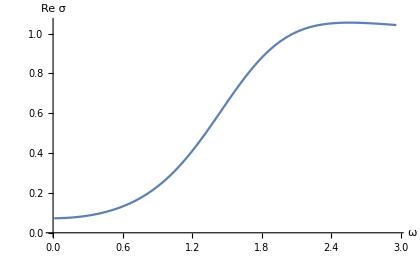

```mathematica
p1 = ListLinePlot[ SigmaData[[All,1;;2]] , AxesLabel->{"ω","Re σ"}, BaseStyle->15]
```

plot of the imaginary part of σ

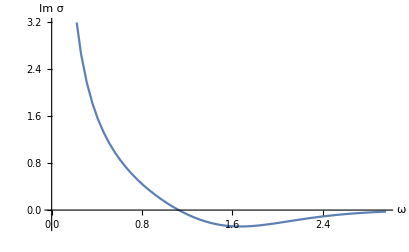

```mathematica
p2 = ListLinePlot[ SigmaData[[All,1;;3;;2]]  , AxesLabel->{"ω","Im σ"}, BaseStyle->15 ]
```

```mathematica
oneover[list_]:= Table[ {list[[i,1]],1/list[[i,2]] }, {i,1,Length[list]} ];
```

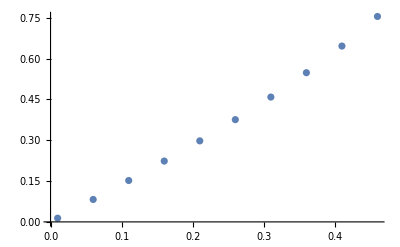

```mathematica
ListPlot[ oneover[ SigmaData[[All,1;;3;;2]] ][[1;;10]]   ]
```

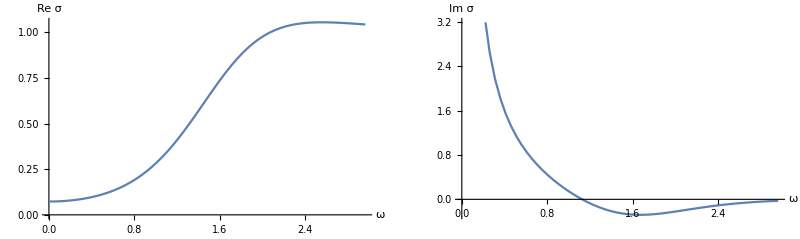

```mathematica
GraphicsRow[{p1,p2}]
```